```mathematica
rawdata=Import[NotebookDirectory[]~~"MonteCarloRun0.csv"]
```

```mathematica
data=Rest[rawdata]
```

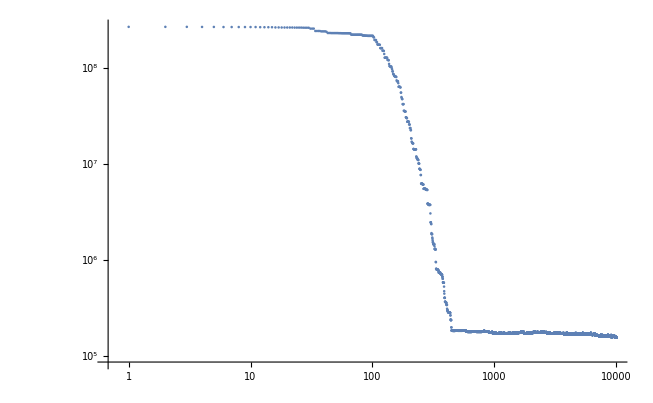

```mathematica
chisqs=data[[All,12]];
ListLogLogPlot[chisqs]
```

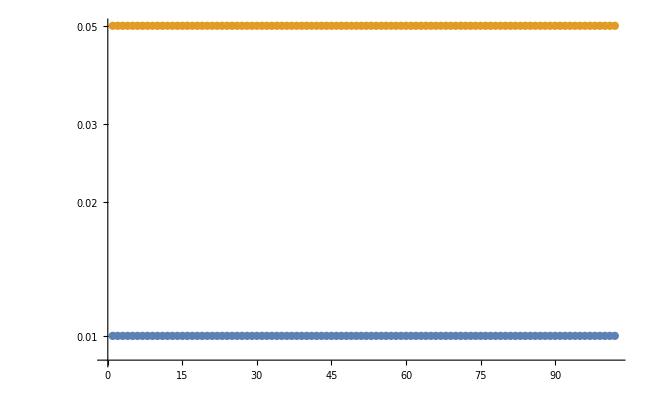

```mathematica
stepsizes=data[[All,13;;14]];
ListLogPlot[Transpose[stepsizes][[All,1;;UpTo[20000];;100]]]
```

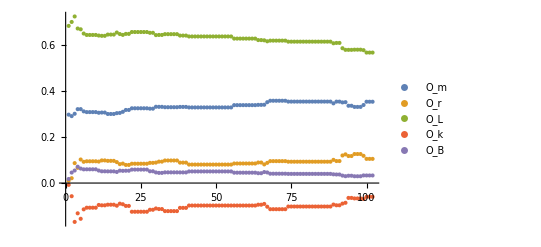

```mathematica
cosmoparams=Transpose[data[[;;;;100,2;;6]]];
ListPlot[cosmoparams,PlotLegends->rawdata[[1,2;;6]]]
```

```mathematica
nvectors=data[[All,9;;11]]
ListPointPlot3D[{nvectors[[;;;;100]],{Last[nvectors]}}]
```

-Graphics3D-